```mathematica
(* Find all prime number p < e^(10) =22026.5...  such that Summatory[Floor[Sqrt[p]]]= Floor[(p+1)/3]. *)
```

```mathematica
l={};
i0=2;
p=Prime[i0];
S=Sum[EulerPhi[i],{i,1,Floor[Sqrt[p]]}];
Print[S];
For[j=i0+1,j<=2500,j++,
p0=p;
p=Prime[j];
S+=Sum[EulerPhi[i],{i,Floor[Sqrt[p0]]+1,Floor[Sqrt[p]]}];
T=Floor[(p+1)/3];
(*Print["(p, Summatory[Floor[Sqrt[p]]], Floor[(p+1)/3]) = (",p, ", ", S, ", ", T, ")"];*)
If[S==T,Print["Compact at p = ",p];AppendTo[l,p]];
]
```

1

Compact at p = 5

Compact at p = 7

Compact at p = 11

Compact at p = 13

Compact at p = 17

Compact at p = 19

Compact at p = 29

Compact at p = 31

Compact at p = 37

Compact at p = 53

Compact at p = 67

Compact at p = 83

Compact at p = 127

Compact at p = 173

```mathematica
l
```

{5,7,11,13,17,19,29,31,37,53,67,83,127,173}

```mathematica
l={};
i0=2;
p=Prime[i0];
S=Sum[EulerPhi[i],{i,1,Floor[Sqrt[p]]+1}];
Print[S];
For[j=i0+1,j<=2500,j++,
p0=p;
p=Prime[j];
S+=Sum[EulerPhi[i],{i,Floor[Sqrt[p0]]+2,Floor[Sqrt[p]]+1}];
T=Floor[(p+1)/3];
(*Print["(p, Summatory[Floor[Sqrt[p]]], Floor[(p+1)/3]) = (",p, ", ", S, ", ", T, ")"];*)
If[S==T,Print["v+1 Compact at p = ",p];AppendTo[l,p]];
]
```

2

v+1 Compact at p = 97

v+1 Compact at p = 137

v+1 Compact at p = 139

v+1 Compact at p = 191

v+1 Compact at p = 193

v+1 Compact at p = 239

v+1 Compact at p = 241

v+1 Compact at p = 307

v+1 Compact at p = 359

v+1 Compact at p = 383

v+1 Compact at p = 419

v+1 Compact at p = 421

v+1 Compact at p = 449

v+1 Compact at p = 541

v+1 Compact at p = 599

v+1 Compact at p = 601

v+1 Compact at p = 691

v+1 Compact at p = 809

v+1 Compact at p = 811

v+1 Compact at p = 971

v+1 Compact at p = 1031

v+1 Compact at p = 1033

v+1 Compact at p = 1297

```mathematica
SpecialPolygon[97]
```

Complete at p = 97

{False,{1,10,9,8,7,6,11,5,9,4,11,7,3,8,5,7,9,2,9,7,5,8,3,10,7,4,9,5,6,7,8,9,1},{7,8,1,2,3,11,12,4,-2,13,14,8,-3,5,13,7,1,6,9,11,4,-3,9,10,12,-2,5,14,2,3,6,10}}

```mathematica
Summatory[100]
```

3044

```mathematica
Summatory[Floor[Sqrt[173]]]
```

58

```mathematica
Floor[174/3]
```

58

```mathematica
Exp[10]//N
```

22026.5

```mathematica
Prime[2500]
```

22307

```mathematica
2^(15)//N
```

32768.

```mathematica
Prime[15400]
```

168863

```mathematica
2^18//N
```

262144.

Found at q = 2

Found at q = 4

Found at q = 3

Found at q = 9

Found at q = 5

Found at q = 25

Found at q = 7

Found at q = 49

Found at q = 11

Found at q = 13

Found at q = 17

Found at q = 19

Found at q = 29

Found at q = 31

Found at q = 37

Found at q = 53

Found at q = 67

Found at q = 83

Found at q = 127

Found at q = 173

```mathematica
PrimeFactors[n_Integer]:=Flatten[Take[Transpose[FactorInteger[n]],1]];
GG0Index[n_Integer]:=
Module[{l,s,i},
l=PrimeFactors[n];
s=n;
For[i=1,i<=Length[l],i++,
s*=1+1/l[[i]];
];
Return[s];
];
v2[n_Integer]:=
Module[{l,s,i,r,p},
If[Mod[n,4]==0,Return[0]];
l=PrimeFactors[n];
s=1;

For[i=1,i<=Length[l],i++,
p=l[[i]];
If[p==2,Continue[]];
r=Mod[l[[i]],4];

If[r==3,Return[0],s*=2];
];
Return[s];
];
v3[n_Integer]:=
Module[{l,s,i,r},
If[Mod[n,9]==0,Return[0]];
l=PrimeFactors[n];
s=1;

For[i=1,i<=Length[l],i++,

r=Mod[l[[i]],3];

If[r==2,Return[0],If[r==1,s*=2]];
];
Return[s];
];
Summatory[m_Integer]:=Sum[EulerPhi[i],{i,1,m}];
```

```mathematica
Summatory[4]
```

6

```mathematica
p=23;
Print[Floor[(p+1)/3]]
```

8

```mathematica
Summatory[Floor[Sqrt[p]]]
```

6

```mathematica
Floor[Sqrt[4p/3]]
```

5

```mathematica
Denominator[FareySequence[Floor[Sqrt[p]]]]
```

{1,4,3,2,3,4,1}

```mathematica
v2[480]
```

0

```mathematica
v3[81]
```

0

```mathematica
v2[81]
```

0

```mathematica
v2[121]
```

0

```mathematica
l3={};
For[i=10000,i<=50000,i++,
AppendTo[l3,v3[i]];
];
Print[Max[l3]];
```

8

```mathematica
v3[7*13*19*31*37]
```

32

```mathematica
l3
```

{2,0,1,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,2,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,4,0,2,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,0,0,0,4,0,0,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,4,0,2,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,2,0,4,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,2,0,2,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,4,0,0,0,4,0,0,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,4,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,4,0,2,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,0,0,0,2,0,0,0,0,0,4,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,2,0,2,0,0,0,4,0,0,0,0,0,2,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,4,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,4,0,2,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,2,0,4,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,4,0,0,0,0,0,2,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,0,0,0,4,0,0,0,0,0,2,0,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,0,0,0,2,0,0,0}

```mathematica
GG0Index[480]
```

1152

```mathematica
PrimeFactors[73]
```

{2,3,5}

```mathematica
v3[15]
```

1

1

0

1

2

zero factor!

0

```mathematica
v3[71]
```

0

```mathematica
v3[73]
```

0

```mathematica
Mod[12,3]
```

0

```mathematica
For[i=1,i<=15400,i++,
p=Prime[i];
For[r=1,r<=17,r++,
q=p^r;
If[q>168000,Break[]];
If[Summatory[Floor[Sqrt[q]]]==Floor[(q+q/p)/3],Print["Found at q = ", q]];
]
];
```

```mathematica
Summatory[10]
```

32

```mathematica
GG0Index[10]
```

18

```mathematica
For[n=1,n<=1000000,n++,
If[Summatory[Floor[Sqrt[n]]]==(GG0Index[n]-v3[n])/3,
Print["Found at n = ", n]];
]
```

Found at n = 2

Found at n = 3

Found at n = 4

Found at n = 5

Found at n = 7

Found at n = 9

Found at n = 11

Found at n = 13

Found at n = 17

Found at n = 19

Found at n = 25

Found at n = 29

Found at n = 31

Found at n = 37

Found at n = 49

Found at n = 53

Found at n = 67

Found at n = 83

Found at n = 127

Found at n = 173

```mathematica
v3multi[t_Integer]:=
Module[{},
If[t<=0,Return[1]];
If[t==1,Return[3]];
If[t>1,Return[(6t-5)v3multi[t-1]]];
];
```

```mathematica
v3multi[5]
```

129675

```mathematica
3*7*13*19
```

5187

```mathematica
16^3
```

4096

```mathematica
compare[m_Integer]:=3 m^3/Pi^2+2m Log[m]-Summatory[m];
```

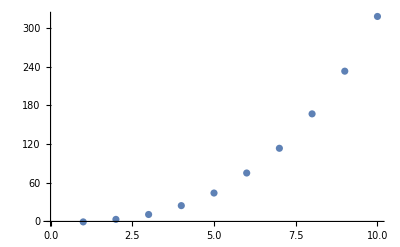

```mathematica
ListPlot[Table[compare[m],{m,1,10}]]
```

```mathematica
compare[1]//N
```

-0.696036

```mathematica
gg[x_Real]:=(x-Sqrt[x])/3-3x/Pi^2-Sqrt[x]Log[x];
```

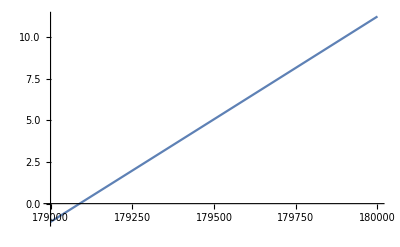

```mathematica
Plot[g[x],{x,179000,180000}]
```

```mathematica
gg[2.]
```

-1.39292

```mathematica
D[(x-Sqrt[x])/3-3x/Pi^2-Sqrt[x]Log[x],x]
```

```mathematica
h[x_Real]:=-3/π^2+1/3 (1-1/(2 √x))-1/(√x)-Log[x]/(2 √x);
```

```mathematica
h[1]
```

-5/6-3/π^2

```mathematica
Simplify[h[x]]
```

1/6 (2-18/π^2-7/(√x)-(3 Log[x])/(√x))

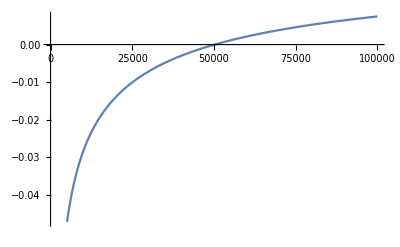

```mathematica
Plot[h[x],{x,2,100000}]
```

```mathematica
h[1.1]
```

General::ivar: 1.1 is not a valid variable.

∂_1.1 (-0.417258)

```mathematica
2^(17)
```

131072

```mathematica
Prime[16350]
```

180077

```mathematica
For[i=1,i<=16350,i++,
p=Prime[i];
For[r=1,r<=17,r++,
q=p^r;
If[q>180000,Break[]];
If[Summatory[Floor[Sqrt[q]]]==Floor[(q+q/p)/3],Print["Found at q = ", q]];
]
];
```

Found at q = 2

Found at q = 4

Found at q = 3

Found at q = 9

Found at q = 5

Found at q = 25

Found at q = 7

Found at q = 49

Found at q = 11

Found at q = 13

Found at q = 17

Found at q = 19

Found at q = 29

Found at q = 31

Found at q = 37

Found at q = 53

Found at q = 67

Found at q = 83

Found at q = 127

Found at q = 173

$Aborted

```mathematica
For[n=1,n<=180000,n++,
If[Summatory[Floor[Sqrt[n]]]==(GG0Index[n]-v3[n])/3,
Print["Found at n = ", n]];
If[Mod[n,10000]==0,Print["n is "n]];
]
```

Found at n = 2

Found at n = 3

Found at n = 4

Found at n = 5

Found at n = 7

Found at n = 9

Found at n = 11

Found at n = 13

Found at n = 17

Found at n = 19

Found at n = 25

Found at n = 29

Found at n = 31

Found at n = 37

Found at n = 49

Found at n = 53

Found at n = 67

Found at n = 83

Found at n = 127

Found at n = 173

10000 n is

20000 n is

30000 n is

40000 n is

50000 n is

60000 n is

70000 n is

80000 n is

90000 n is

100000 n is

110000 n is

120000 n is

130000 n is

140000 n is

150000 n is

160000 n is

170000 n is

180000 n is

```mathematica
For[i=1,i<=1000,i++,
If[PrimeQ[i],Print["i = ",i," and the diff = ",Floor[4Sqrt[i]/Pi]-Floor[Sqrt[i]]]];
];
```

i = 2 and the diff = 0

i = 3 and the diff = 1

i = 5 and the diff = 0

i = 7 and the diff = 1

i = 11 and the diff = 1

i = 13 and the diff = 1

i = 17 and the diff = 1

i = 19 and the diff = 1

i = 23 and the diff = 2

i = 29 and the diff = 1

i = 31 and the diff = 2

i = 37 and the diff = 1

i = 41 and the diff = 2

i = 43 and the diff = 2

i = 47 and the diff = 2

i = 53 and the diff = 2

i = 59 and the diff = 2

i = 61 and the diff = 2

i = 67 and the diff = 2

i = 71 and the diff = 2

i = 73 and the diff = 2

i = 79 and the diff = 3

i = 83 and the diff = 2

i = 89 and the diff = 3

i = 97 and the diff = 3

i = 101 and the diff = 2

i = 103 and the diff = 2

i = 107 and the diff = 3

i = 109 and the diff = 3

i = 113 and the diff = 3

i = 127 and the diff = 3

i = 131 and the diff = 3

i = 137 and the diff = 3

i = 139 and the diff = 4

i = 149 and the diff = 3

i = 151 and the diff = 3

i = 157 and the diff = 3

i = 163 and the diff = 4

i = 167 and the diff = 4

i = 173 and the diff = 3

i = 179 and the diff = 4

i = 181 and the diff = 4

i = 191 and the diff = 4

i = 193 and the diff = 4

i = 197 and the diff = 3

i = 199 and the diff = 3

i = 211 and the diff = 4

i = 223 and the diff = 5

i = 227 and the diff = 4

i = 229 and the diff = 4

i = 233 and the diff = 4

i = 239 and the diff = 4

i = 241 and the diff = 4

i = 251 and the diff = 5

i = 257 and the diff = 4

i = 263 and the diff = 4

i = 269 and the diff = 4

i = 271 and the diff = 4

i = 277 and the diff = 5

i = 281 and the diff = 5

i = 283 and the diff = 5

i = 293 and the diff = 4

i = 307 and the diff = 5

i = 311 and the diff = 5

i = 313 and the diff = 5

i = 317 and the diff = 5

i = 331 and the diff = 5

i = 337 and the diff = 5

i = 347 and the diff = 5

i = 349 and the diff = 5

i = 353 and the diff = 5

i = 359 and the diff = 6

i = 367 and the diff = 5

i = 373 and the diff = 5

i = 379 and the diff = 5

i = 383 and the diff = 5

i = 389 and the diff = 6

i = 397 and the diff = 6

i = 401 and the diff = 5

i = 409 and the diff = 5

i = 419 and the diff = 6

i = 421 and the diff = 6

i = 431 and the diff = 6

i = 433 and the diff = 6

i = 439 and the diff = 6

i = 443 and the diff = 5

i = 449 and the diff = 5

i = 457 and the diff = 6

i = 461 and the diff = 6

i = 463 and the diff = 6

i = 467 and the diff = 6

i = 479 and the diff = 6

i = 487 and the diff = 6

i = 491 and the diff = 6

i = 499 and the diff = 6

i = 503 and the diff = 6

i = 509 and the diff = 6

i = 521 and the diff = 7

i = 523 and the diff = 7

i = 541 and the diff = 6

i = 547 and the diff = 6

i = 557 and the diff = 7

i = 563 and the diff = 7

i = 569 and the diff = 7

i = 571 and the diff = 7

i = 577 and the diff = 6

i = 587 and the diff = 6

i = 593 and the diff = 7

i = 599 and the diff = 7

i = 601 and the diff = 7

i = 607 and the diff = 7

i = 613 and the diff = 7

i = 617 and the diff = 7

i = 619 and the diff = 7

i = 631 and the diff = 6

i = 641 and the diff = 7

i = 643 and the diff = 7

i = 647 and the diff = 7

i = 653 and the diff = 7

i = 659 and the diff = 7

i = 661 and the diff = 7

i = 673 and the diff = 8

i = 677 and the diff = 7

i = 683 and the diff = 7

i = 691 and the diff = 7

i = 701 and the diff = 7

i = 709 and the diff = 7

i = 719 and the diff = 8

i = 727 and the diff = 8

i = 733 and the diff = 7

i = 739 and the diff = 7

i = 743 and the diff = 7

i = 751 and the diff = 7

i = 757 and the diff = 8

i = 761 and the diff = 8

i = 769 and the diff = 8

i = 773 and the diff = 8

i = 787 and the diff = 7

i = 797 and the diff = 7

i = 809 and the diff = 8

i = 811 and the diff = 8

i = 821 and the diff = 8

i = 823 and the diff = 8

i = 827 and the diff = 8

i = 829 and the diff = 8

i = 839 and the diff = 8

i = 853 and the diff = 8

i = 857 and the diff = 8

i = 859 and the diff = 8

i = 863 and the diff = 8

i = 877 and the diff = 8

i = 881 and the diff = 8

i = 883 and the diff = 8

i = 887 and the diff = 8

i = 907 and the diff = 8

i = 911 and the diff = 8

i = 919 and the diff = 8

i = 929 and the diff = 8

i = 937 and the diff = 8

i = 941 and the diff = 9

i = 947 and the diff = 9

i = 953 and the diff = 9

i = 967 and the diff = 8

i = 971 and the diff = 8

i = 977 and the diff = 8

i = 983 and the diff = 8

i = 991 and the diff = 9

i = 997 and the diff = 9